```mathematica
SetDirectory[NotebookDirectory[]];
```

## Uloha 1 - 4-Step AdamBashford

### Init with EEM

{{x→Function[{t},ArcTan[16 t]]}}

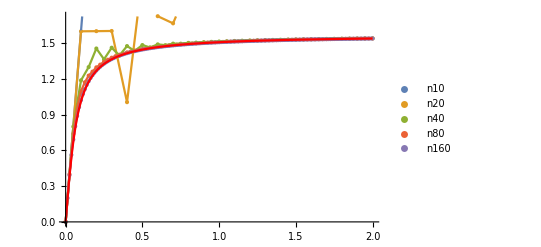

```mathematica
n10 = Import["./outputs/uloha1_adam_bash_4_w_EEM_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_adam_bash_4_w_EEM_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_adam_bash_4_w_EEM_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_adam_bash_4_w_EEM_80n.csv","CSV"];
n160 = Import["./outputs/uloha1_adam_bash_4_w_EEM_160n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20, n40, n80, n160}, PlotLegends->{"n10","n20","n40","n80","n160"}],
ListLinePlot[{n10, n20, n40, n80, n160}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### Init with RK2

{{x→Function[{t},ArcTan[16 t]]}}

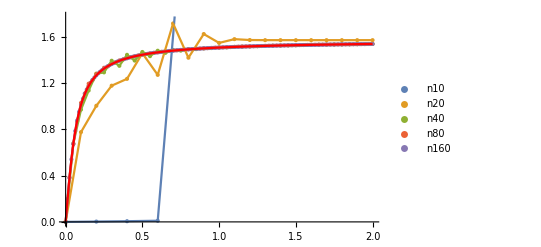

```mathematica
n10 = Import["./outputs/uloha1_adam_bash_4_w_RK2_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_adam_bash_4_w_RK2_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_adam_bash_4_w_RK2_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_adam_bash_4_w_RK2_80n.csv","CSV"];
n160 = Import["./outputs/uloha1_adam_bash_4_w_RK2_160n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20, n40, n80, n160}, PlotLegends->{"n10","n20","n40","n80","n160"}],
ListLinePlot[{n10, n20, n40, n80, n160}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### Init with SSPRK3

{{x→Function[{t},ArcTan[16 t]]}}

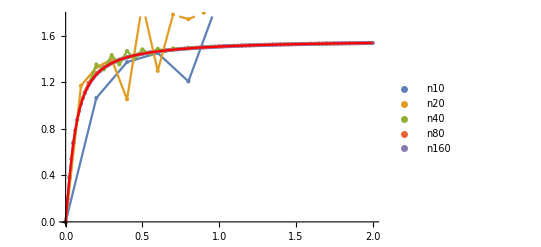

```mathematica
n10 = Import["./outputs/uloha1_adam_bash_4_w_SSPRK3_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_adam_bash_4_w_SSPRK3_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_adam_bash_4_w_SSPRK3_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_adam_bash_4_w_SSPRK3_80n.csv","CSV"];
n160 = Import["./outputs/uloha1_adam_bash_4_w_SSPRK3_160n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20, n40, n80, n160}, PlotLegends->{"n10","n20","n40","n80","n160"}],
ListLinePlot[{n10, n20, n40, n80, n160}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### Druhá rovnica s SSPRK3

{{x→Function[{t},√(-1+2 ⅇ^t)]}}

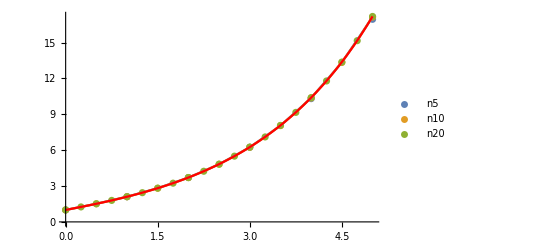

```mathematica
n5 = Import["./outputs/uloha1_adam_bash_4_w_SSPRK3_2_5n.csv","CSV"];n10 = Import["./outputs/uloha1_adam_bash_4_w_SSPRK3_2_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_adam_bash_4_w_SSPRK3_2_20n.csv","CSV"];
DSolve[{x'[t]==(x[t]^2+1)/(2 x[t]), x[0]==1},x,{t,0,5}]
Show[
ListPlot[{n5, n10, n20}, PlotLegends->{"n5","n10","n20"}],
ListLinePlot[{n10, n20}],
Plot[Evaluate[x[t]/.%],{t,0,5}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 2 - Adams-Bashforth 2-step

{{x→Function[{t},ArcTan[16 t]]}}

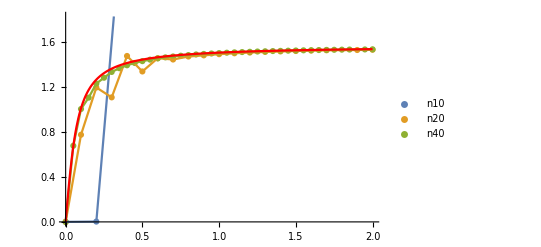

```mathematica
n10 = Import["./outputs/uloha2_adam_bash_10n.csv","CSV"];
n20 = Import["./outputs/uloha2_adam_bash_20n.csv","CSV"];
n40 = Import["./outputs/uloha2_adam_bash_40n.csv","CSV"];
n80 = Import["./outputs/uloha2_adam_bash_80n.csv","CSV"];
n160 = Import["./outputs/uloha2_adam_bash_160n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20, n40}, PlotLegends->{"n10","n20","n40","n80"}],
ListLinePlot[{n10, n20, n40}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 3 - Adams-Bashfort 3-step

### With EEM

{{x→Function[{t},ArcTan[16 t]]}}

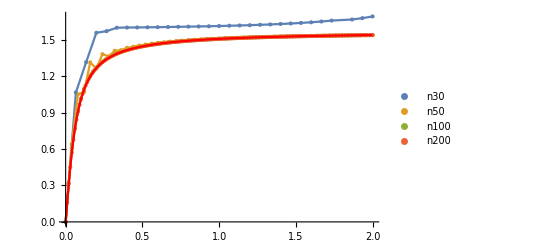

```mathematica
n30 = Import["./outputs/uloha3_adam_bash_EEM_30n.csv","CSV"];
n50 = Import["./outputs/uloha3_adam_bash_EEM_50n.csv","CSV"];
n100 = Import["./outputs/uloha3_adam_bash_EEM_100n.csv","CSV"];
n200 = Import["./outputs/uloha3_adam_bash_EEM_200n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n30, n50, n100, n200}, PlotLegends->{"n30","n50","n100","n200"}],
ListLinePlot[{n30, n50, n100, n200}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### With RK2

{{x→Function[{t},ArcTan[16 t]]}}

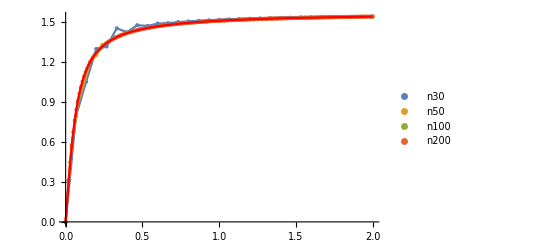

```mathematica
n30 = Import["./outputs/uloha3_adam_bash_RK2_30n.csv","CSV"];
n50 = Import["./outputs/uloha3_adam_bash_RK2_50n.csv","CSV"];
n100 = Import["./outputs/uloha3_adam_bash_RK2_100n.csv","CSV"];
n200 = Import["./outputs/uloha3_adam_bash_RK2_200n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n30, n50, n100, n200}, PlotLegends->{"n30","n50","n100","n200"}],
ListLinePlot[{n30, n50, n100, n200}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```